```mathematica
Manipulate[
Labeled[
Graphics[
{
EdgeForm@Thick,
Blue,
Parallelogram[{0,0},{{a,b},{c,d}}]
},
Axes->True,
PlotRange->{{0,20},{0,20}}
],
a d - b c,
LabelStyle->Directive[Blue]
],
{{a,9},1,10,1,Appearance->"Labeled"},
{{b,4},1,10,1,Appearance->"Labeled"},
{{c,8},1,10,1,Appearance->"Labeled"},
{{d,10},1,10,1,Appearance->"Labeled"}
]
```

1.B)

a,b,c, and d each have 11 possible values (0-10), so to get all the different combinations of vectors (and therefore all the possible parallelograms) you have to raise 11^4, which equals 14,641.

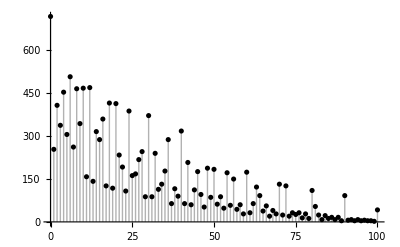

```mathematica
ListPlot[
Tally[
Flatten[
Table[
Abs[a d - b c],
{a,0,10,1},
{b,0,10,1},
{c,0,10,1},
{d,0,10,1}
]
]
],
Filling->Bottom,
PlotStyle->Black
]
```

```mathematica
TableForm[
Partition[
Map[
Labeled[
Graphics[
{
EdgeForm[Thick],Red,
Parallelogram[{0,0},{{#[[1]],#[[2]]},{#[[3]],#[[4]]}}]
},
Axes->True,
PlotRange->{{0,20},{0,20}},
ImageSize->80,
TicksStyle->5
],
{{#[[1]],#[[2]]},{#[[3]],#[[4]]}},
LabelStyle->6
]&,
Select[
Flatten[
Table[
{a,b,c,d,Abs[a d - b c]},
{a,0,10,1},
{b,0,10,1},
{c,0,10,1},
{d,0,10,1}
],
3
],
#[[5]]==100&
]
],
6
]
]
```

-Graphics-{{0,10},{10,0}} | -Graphics-{{0,10},{10,1}} | -Graphics-{{0,10},{10,2}} | -Graphics-{{0,10},{10,3}} | -Graphics-{{0,10},{10,4}} | -Graphics-{{0,10},{10,5}}
-Graphics-{{0,10},{10,6}} | -Graphics-{{0,10},{10,7}} | -Graphics-{{0,10},{10,8}} | -Graphics-{{0,10},{10,9}} | -Graphics-{{0,10},{10,10}} | -Graphics-{{1,10},{10,0}}
-Graphics-{{2,10},{10,0}} | -Graphics-{{3,10},{10,0}} | -Graphics-{{4,10},{10,0}} | -Graphics-{{5,10},{10,0}} | -Graphics-{{6,10},{10,0}} | -Graphics-{{7,10},{10,0}}
-Graphics-{{8,10},{10,0}} | -Graphics-{{9,10},{10,0}} | -Graphics-{{10,0},{0,10}} | -Graphics-{{10,0},{1,10}} | -Graphics-{{10,0},{2,10}} | -Graphics-{{10,0},{3,10}}
-Graphics-{{10,0},{4,10}} | -Graphics-{{10,0},{5,10}} | -Graphics-{{10,0},{6,10}} | -Graphics-{{10,0},{7,10}} | -Graphics-{{10,0},{8,10}} | -Graphics-{{10,0},{9,10}}
-Graphics-{{10,0},{10,10}} | -Graphics-{{10,1},{0,10}} | -Graphics-{{10,2},{0,10}} | -Graphics-{{10,3},{0,10}} | -Graphics-{{10,4},{0,10}} | -Graphics-{{10,5},{0,10}}
-Graphics-{{10,6},{0,10}} | -Graphics-{{10,7},{0,10}} | -Graphics-{{10,8},{0,10}} | -Graphics-{{10,9},{0,10}} | -Graphics-{{10,10},{0,10}} | -Graphics-{{10,10},{10,0}}

```mathematica
detOpps[2] = 3;
detOpps[3] = 14;
detOpps[n_]:=n detOpps[n-1] +2n-1
```

```mathematica
TableForm[
Table[
{x,detOpps[x]},
{x,2,30,1}
]
]
```

2 | 3
3 | 14
4 | 63
5 | 324
6 | 1955
7 | 13698
8 | 109599
9 | 986408
10 | 9864099
11 | 108505110
12 | 1302061343
13 | 16926797484
14 | 236975164803
15 | 3554627472074
16 | 56874039553215
17 | 966858672404688
18 | 17403456103284419
19 | 330665665962403998
20 | 6613313319248079999
21 | 138879579704209680020
22 | 3055350753492612960483
23 | 70273067330330098091154
24 | 1686553615927922354187743
25 | 42163840398198058854693624
26 | 1096259850353149530222034275
27 | 29599015959535037315994925478
28 | 828772446866981044847857913439
29 | 24034400959142450300587879489788
30 | 721032028774273509017636384693699